Part::partw: Part 3 of {0.03,1.63802} does not exist.

Part::partw: Part 3 of {0.03,1.43955} does not exist.

Part::partw: Part 3 of {0.03,1.11017} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of {0.03,1.63802} does not exist.

Part::partw: Part 4 of {0.03,1.43955} does not exist.

Part::partw: Part 4 of {0.03,1.11017} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

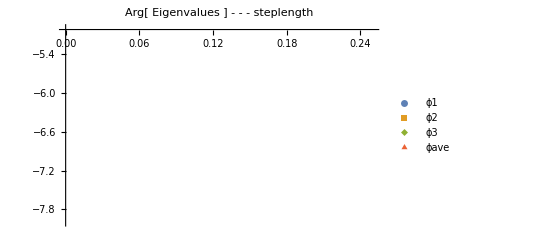

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/steplength/teststeplength_dfromnorm","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];



ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - steplength",PlotRange->{{0,0.25},{-8,-5}}]
```